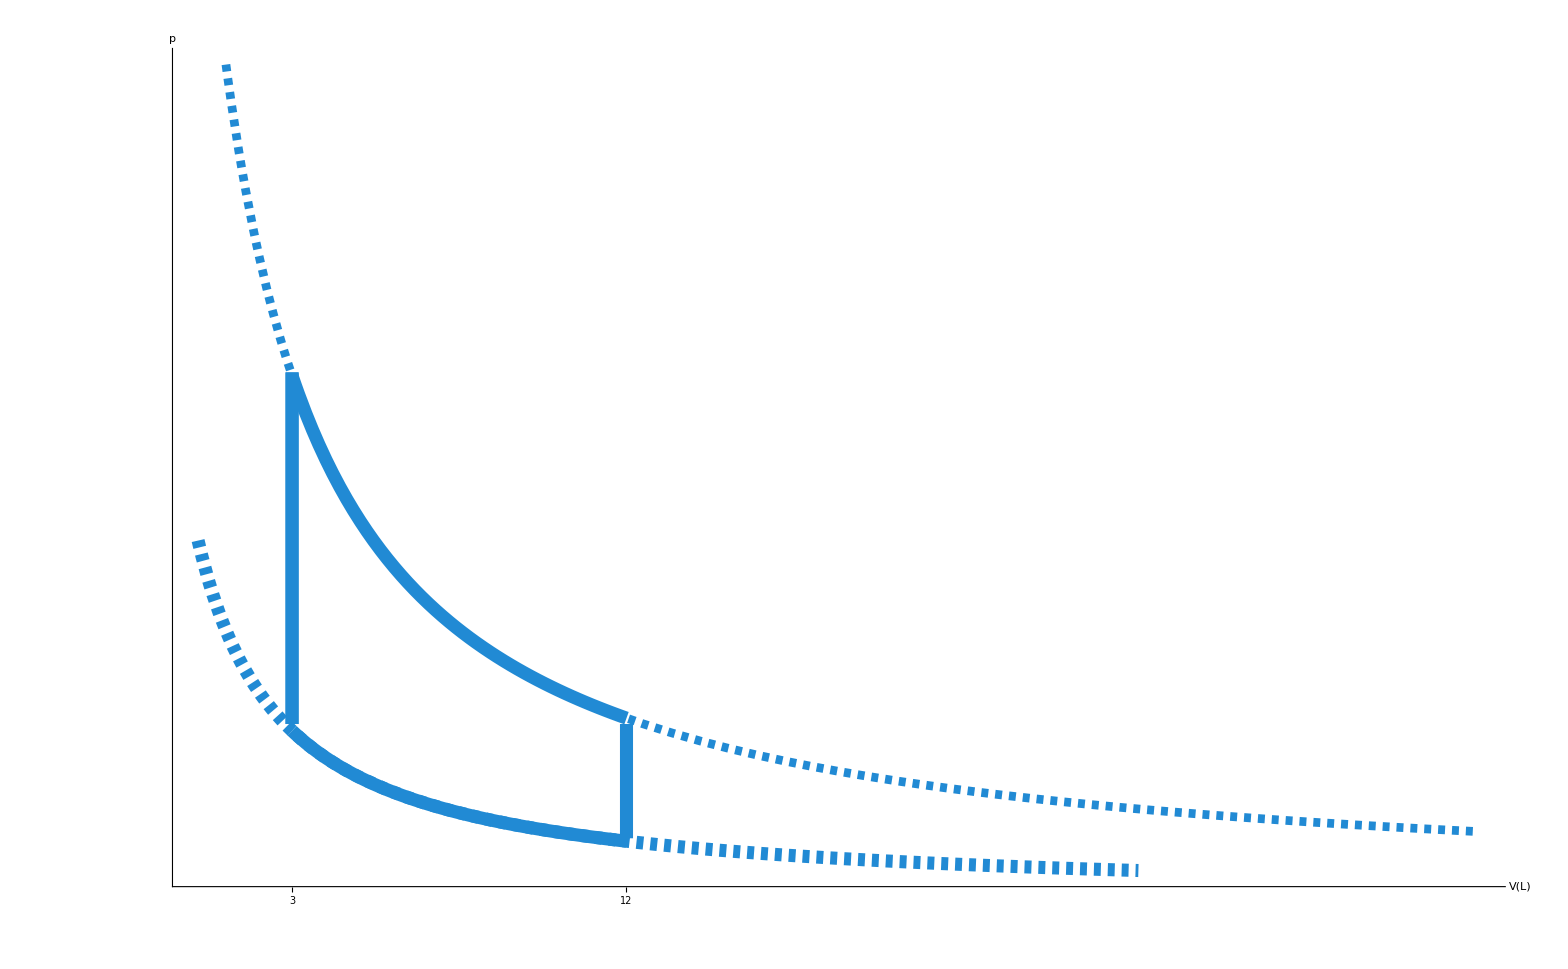

```mathematica
f[x_]:=0.5/x
g[x_]:=1.55/x
h[x_]:=0.5/x
i[x_]:=1.55/x
Show[{Plot[f[x],{x,0.52,1.5},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[g[x],{x,0.52,1.5},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[h[x],{x,0,3},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"],Dashed}],Plot[i[x],{x,0,4},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V[L],p},AxesStyle-> Thick,Epilog->{Thickness[0.006],RGBColor["#218ad4"],Line[{{0.52,1},{0.52,3}}],Line[{{1.5,0.35},{1.5,1}}],Line[{{0.52,1},{0.52,3}}]},Ticks->{{{0.52,3},{1.5,12}}, {{8,8},{12,12}}},ImageSize->2000]
```

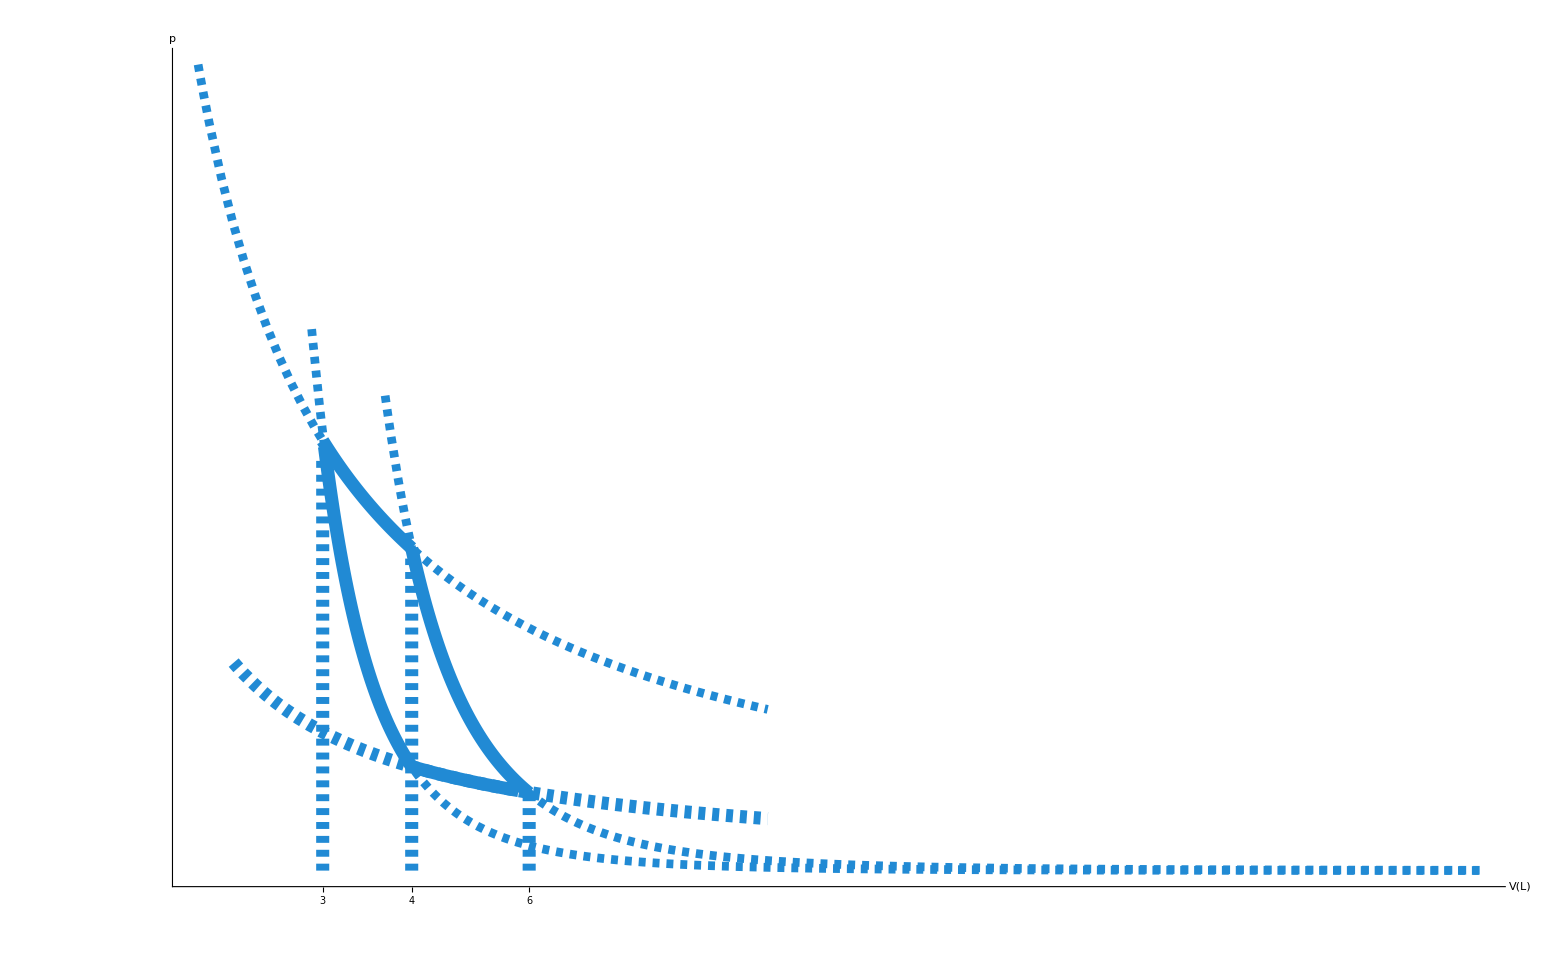

```mathematica
f[x_]:=0.5/x
g[x_]:=1.55/x
h[x_]:=0.5/x
i[x_]:=1.55/x
j[x_]:=0.5/x^5
k[x_]:=1.55/x^5
l[x_]:=0.5/x^5
m[x_]:=1.55/x^5
Show[{Plot[f[x],{x,1,1.3},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[g[x],{x,0.75,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[h[x],{x,0.5,2},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"],Dashed}],Plot[i[x],{x,0.4,2},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[j[x],{x,0.2,4},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[k[x],{x,0.5,4},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[l[x],{x,0.755,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[m[x],{x,1,1.33},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V[L],p},AxesStyle-> Thick,Ticks->{{{0.75,3},{1,4},{1.33,6}}, {{8,8},{12,12}}},ImageSize->2000,Epilog->{Thickness[0.006],RGBColor["#218ad4"],Dashed,Line[{{0.75,0},{0.75,2}}],Line[{{1,0},{1,1.5}}],Line[{{1.33,0},{1.33,0.4}}]}]
```